#### Draw mesh

```mathematica
SetDirectory[NotebookDirectory[]]
(*SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop-Debug"}]]*)
(*SetDirectory["build-converterUNV-Desktop-u041eu0442u043bu0430u0434u043au0430"]*)
(*SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop_Qt_5_10_1_MinGW_32bit-Debug"}]]*)
```

/home/v.korchagova/Документы/BMSTU/RKDG2D

```mathematica
mesh=Import["mesh2D","Table"];
```

```mathematica
(*nodes*)
offset=2;
nNodes=mesh[[offset,1]]
nodes=Table[mesh[[i]],{i,offset+1,nNodes+offset}];
(*edges*)
offset=3+nNodes+1+1;
nEdgesBoundary=mesh[[offset,1]]
nEdges=mesh[[offset+1,1]]
edges=Table[mesh[[i]],{i,offset+2,nEdges+offset+1}];
(*cells*)
offset = offset +nEdges+4;
nCells=mesh[[offset]][[1]]
cells=Table[mesh[[i]],{i,offset+1,nCells+offset}];
(*cell centers*)
offset = offset +nCells+4;
cellCenters=Table[mesh[[i]],{i,offset,nCells+offset-1}];
(*adjoint cells for edges*)
offset = nCells+offset+5;
edgeAdj=Table[mesh[[i]],{i,offset,nEdges+offset-3}];

(*edge normals*)
offset = nEdges+offset+1;
edgeNormals=Table[mesh[[i]],{i,offset,nEdges+offset-1}];
```

961

120

1860

900

```mathematica
(*patches*)
offset=offset+nEdges+2;
nPatches=mesh[[offset]][[1]]
offset = offset+1;
patchNames={};
patchEdgeGroups={};
For[i=1,i≤nPatches, ++i,
{
patchNames=Append[patchNames,mesh[[offset,1]]];
(*Print[patchNames];*)
nEdgesInPatch=mesh[[offset+1,1]];
(*Print[nEdgesInPatch];*)
patchEdgeGroups = Append[patchEdgeGroups,Table[mesh[[i,1]],{i,offset+2,offset+1+nEdgesInPatch}]];
offset=offset+2+nEdgesInPatch;
(*Print[offset];*)
}];
patchNames
```

1

{Group_1}

```mathematica
(*drawing functions*)
```

```mathematica
drawNode[iNode_]:=Point[nodes[[iNode]]];
drawEdgeArrow[iEdge_]:=Arrow[{nodes[[edges[[iEdge,1]]]],nodes[[edges[[iEdge,2]]]]}];
drawEdgeLine[iEdge_]:=Arrow[{nodes[[edges[[iEdge,1]]]],nodes[[edges[[iEdge,2]]]]}];
drawEdgeNormal[iEdge_]:=Arrow[{(nodes[[edges[[iEdge,1]]]]+nodes[[edges[[iEdge,2]]]])/2,(nodes[[edges[[iEdge,1]]]]+nodes[[edges[[iEdge,2]]]])/2+edgeNormals[[i]]*0.25*Norm[{nodes[[edges[[iEdge,2]]]]-nodes[[edges[[iEdge,1]]]]},2]}];
drawCell[iCell_]:=Polygon[Table[nodes[[cells[[iCell,i]]]],{i,2,cells[[iCell,1]]+1}]];
drawPatch[color_,iPatch_]:={color,Table[drawEdgeLine[patchEdgeGroups[[i,j]]],{j,1,Length[patchEdgeGroups[[i]]]}]};
getCellNodes[iCell_]:=Table[nodes[[cells[[iCell,i]]]],{i,2,cells[[iCell,1]]+1}];
(*areas*)
areas=Table[Area@drawCell[iCell],{iCell,nCells}];
```

```mathematica
(*pictures*)
```

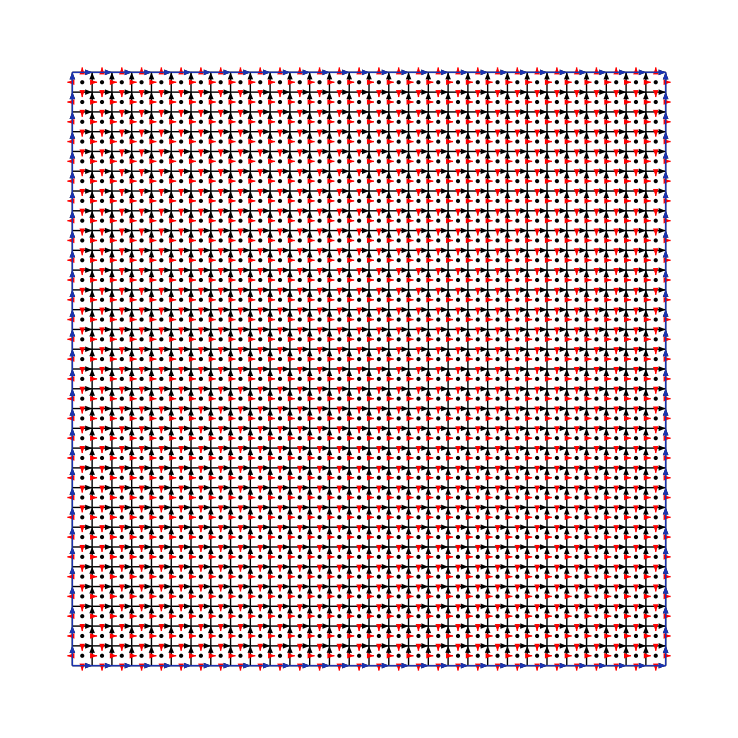

```mathematica
Graphics[{Black,
Table[Point[{cellCenters[[i]]}],{i,1,nCells}],
Table[drawEdgeArrow[i],{i,1,nEdges}],
Red,Arrowheads[0.02],
Table[drawEdgeNormal[i],{i,1,nEdges}],Thick,
Table[drawPatch[RGBColor[i*0.1,i*0.2,i*0.7],i],{i,1,nPatches}]}]
```

```mathematica
Manipulate[Graphics[{Black,Arrowheads[0.02],
Table[drawEdgeArrow[i],{i,1,p}]},PlotRange->All],{p,1,120,1}]
```

```mathematica
Manipulate[Graphics[{EdgeForm[Black],Cyan,
Table[drawCell[i],{i,1,p}],Black,
Table[Point[{cellCenters[[i]]}],{i,1,p}]
},PlotRange->All],{p,1,nCells,1}]
```

```mathematica
gp={{1.780570883290582,-0.07783737235890338},{1.758429656970117,-0.2904930283710848},{1.206180810346533,-0.05103703891300475},{1.192126990569359,-0.1904728222912036}}
Graphics[{EdgeForm[Black],Cyan,drawCell[1],Black,
Point[{cellCenters[[1]]}],Point[{0.660924,-0.067948}],Table[Point[gp[[i]]],{i,4}],Red,Point[cc]}]
```

{{1.78057,-0.0778374},{1.75843,-0.290493},{1.20618,-0.051037},{1.19213,-0.190473}}

-Graphics-

```mathematica
drawCell[1]
```

Polygon[{{-0.5,0.5},{-0.5,0.466667},{-0.466667,0.466667},{-0.466667,0.5}}]

```mathematica
cc={Integrate[x,{x,y}∈ drawCell[1]],Integrate[y,{x,y}∈ drawCell[1]]}/Area@drawCell[1]
```

{-0.483333,0.483333}

```mathematica
Table[drawNode[i],{i,{cells[[1,2;;4]]}}]
```

{Point[{{-0.5,0.5},{-0.5,0.466667},{-0.466667,0.466667}}]}

```mathematica
Graphics[{Black,
Table[drawNode[i],{i,{cells[[1,2;;5]]}}]}]
```

-Graphics-

```mathematica
Manipulate[Graphics[{Black,
Table[drawNode[i],{i,{cells[[iCell,2;;2+p]]}}]},PlotRange->Full],{p,0,cells[[iCell,1]]-1,1},{iCell,1,nCells}]
```

#### Basis functions

```mathematica
phi[r_List,iCell_]:={1.0/(√areas[[iCell]]), (r[[1]]-cellCenters[[iCell,1]])/(areas[[iCell]]/(2 √3)),(r[[2]]-cellCenters[[iCell,2]])/(areas[[iCell]]/(2 √3))};
(*phi[r_List,nCell_]:={1.0, r[[1]]-cellCenters[[nCell,1]],r[[2]]-cellCenters[[nCell,2]]};*)
```

```mathematica
gram=Table[Integrate[phi[{x,y},1][[k]]*phi[{x,y},1][[j]],{x,y}∈Polygon[getCellNodes[1]]],{k,3},{j,3}];
gram//MatrixForm
eig=Eigenvalues[gram]
eig[[1]]/eig[[3]]
Det[gram]
```

(1. | 4.05231×10^-15 | -4.05231×10^-15
4.05231×10^-15 | 1. | -5.17401×10^-13
-4.05231×10^-15 | -5.17401×10^-13 | 1.)

{1.,1.,1.}

1.

1.

```mathematica
GetSol[r_List,nCell_,nSol_]:=Sum[alpha[[nCell,nSol,p]]*phi[r,nCell][[p]],{p,1,numFF}]
```

```mathematica
GetSolGraphics[iCell_,nSol_]:=Module[{cNodes},
(cNodes=Table[nodes[[cells[[iCell,i]]]],{i,2,cells[[i,1]]+1}];
Return[Polygon[Table[{cNodes[[i,1]],cNodes[[i,2]],(GetSol[cNodes[[i]],iCell,nSol]-1)1000000},{i,1,cells[[i,1]]}]]]
)]
GetSolGlobal[iCell_,nSol_]:=Module[{cNodes},
(cNodes=Table[nodes[[cells[[iCell,i]]]],{i,2,cells[[i,1]]+1}];
Return[Table[{cNodes[[i,1]],cNodes[[i,2]],GetSol[cNodes[[i]],iCell,nSol]},{i,1,cells[[i,1]]}]]
)]
```

#### Draw solution

```mathematica
(*SetDirectory[FileNameJoin[{ParentDirectory[],"build-RKDG2D-Desktop-u041eu0442u043bu0430u0434u043au0430"}]]*)
SetDirectory[FileNameJoin[{ParentDirectory[],"build-RKDG2D-Desktop-Debug"}]]
```

/home/v.korchagova/Документы/BMSTU/build-RKDG2D-Desktop-Debug

```mathematica
coeffs=Import["alphaCoeffs/0.997912","Table"];
numFF=3;
alpha=Table[Partition[coeffs[[i]],numFF],{i,1,nCells}];
```

```mathematica
Graphics3D[ParallelTable[GetSolGraphics[i,1],{i,1,nCells}]]
```

-Graphics3D-

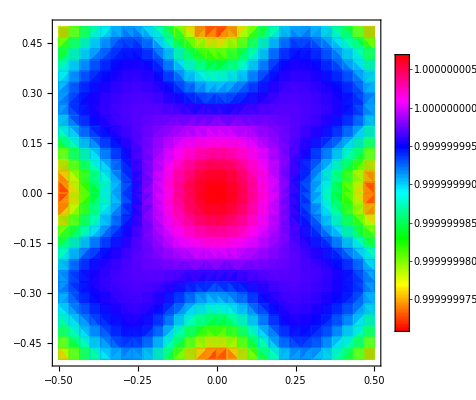

```mathematica
ListDensityPlot[Table[GetSolGlobal[i,1],{i,1,nCells}],ColorFunction->Hue,PlotRange->Full,InterpolationOrder->1,PlotLegends->Automatic,BoundaryStyle->Black]
```